1-2 Floor[Log[-1+v]/(Log[2] (2-Log[3]/Log[2]))]+Floor[(Floor[Log[-1+v]/(Log[2] (2-Log[3]/Log[2]))] Log[3])/Log[2]+Log[v]/Log[2]]

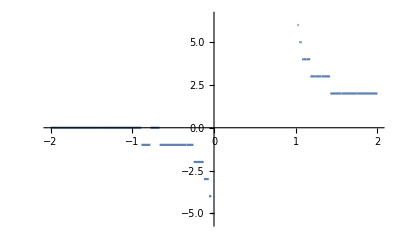

```mathematica
Remove[f,v,x,y];
f[v_]:=Floor[Floor[Log2[v-1]/(2-Log2[3])]*Log2[3]+Log2[v]]+1-2*Floor[Log2[v-1]/(2-Log2[3])];
Print[f[v]];
Plot[f[x],{x,-2,2}]
```